## Matt Meyers, Computer Assignment 2 PHYS 309-010, 10/30/15 Part A

```mathematica
P[t_,v_]:=(8*t)/(3*v-1)-3/(v^2)
G[t_,v_]:=-t*Log[3*v-1]+t/(3*v-1)-9/(4*v)
```

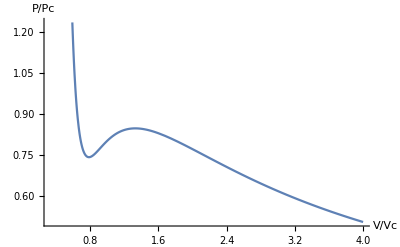

```mathematica
Plot[P[.95,v],{v,1/3,4},AxesLabel->{V/Vc,P/Pc}]
```

In order to find the pressure where the phase transition occurs, the horizontal line can be moved up and down until the two areas enclosed by the horizontal line and the isotherm are equal.  In other words, the difference of the areas should be zero (or close to zero).  This occurs at around p = .8119.  This value is the vapor pressure.

-0.0000216467

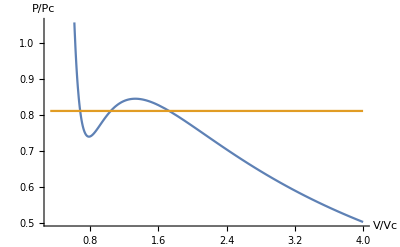

```mathematica
p1=.8119;
{v01,v02,v03}=Values[NSolve[P[.95,v]==p1,v]];
Integrate[p1-P[.95,v],{v,v01[[1]],v02[[1]]}]-Integrate[P[.95,v]-p1,{v,v02[[1]],v03[[1]]}]
Plot[{P[.95,v],p1},{v,1/3,4},AxesLabel->{V/Vc,P/Pc}]
```

Plotting the Gibb’s free energy versus the pressure shows a parametric curve that crosses itself.  As shown by the vertical line p = .8119, the parametric curve crosses itself at p = .8119.  This means the vapor pressure is indeed p = .8119 as predicted before.

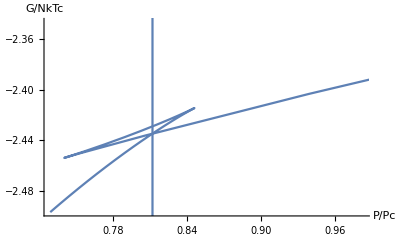

```mathematica
plot01=ParametricPlot[{P[.95,v],G[.95,v]},{v,0,2.25}];
plot02=ParametricPlot[{.8119,t},{t,0,-10}];
Show[{plot01,plot02},AxesLabel->{P/Pc,G/NkTc}]
```

## Part B

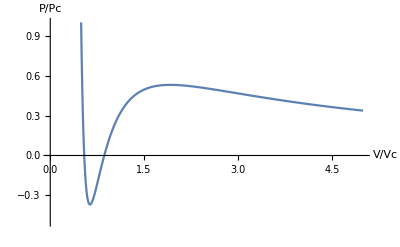

```mathematica
Plot[P[.8,v],{v,1/3,5},PlotRange->{-.5,1},AxesLabel->{V/Vc,P/Pc}]
```

The same process was used here to find the vapor pressure.  In this case, p = .3833.

0.000225268

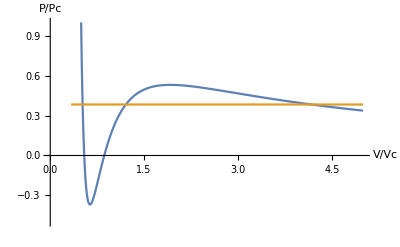

```mathematica
p2=.3833;
{v11,v12,v13}=Values[NSolve[P[.8,v]==p2,v]];
Integrate[p2-P[.8,v],{v,v11[[1]],v12[[1]]}]-Integrate[P[.8,v]-p2,{v,v12[[1]],v13[[1]]}]
Plot[{P[.8,v],p2},{v,1/3,5},PlotRange->{-.5,1},AxesLabel->{V/Vc,P/Pc}]
```

The vertical line p = .3833 shows the parametric curve crosses itself at p = .3833 as expected.

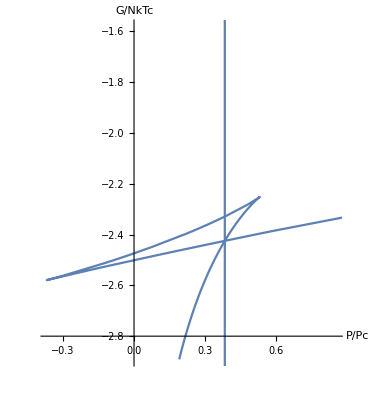

```mathematica
plot11=ParametricPlot[{P[.8,v],G[.8,v]},{v,0,10}];
plot12=ParametricPlot[{.3833,t},{t,0,-10}];
Show[{plot11,plot12},AxesLabel->{P/Pc,G/NkTc}]
```

## Part C

The van der Waal’s constants for water and carbon dioxide are in the following table.

```mathematica
{{, a
(J m^3), b
(m^3)}, {Subscript[H, 2] O, 1.5196 x10^-48, 5.0498 x10^-29}, {Subscript[CO, 2], 1.0052 x10^-48, 7.0930 x10^-29}}
```

```mathematica
aw=1.5196*10^(-48);
bw=5.0498*10^(-29);
ac=1.0052*10^(-48);
bc=7.0930*10^(-29);
k=1.381*10^(-23);
```

The critical temperature depends only on a and b.  Therefore, it will be the same for both parts a and b of this assignment.

```mathematica
Tc[a_,b_]:=(8*a)/(27*b*k)
Tcw=Tc[aw,bw]
Tcc=Tc[ac,bc]
```

645.636

304.057

The critical temperature of water is 645.636 K and the critical temperature of carbon dioxide is 304.057 K.

The temperature is equal to T_c* t.  For part a, t = .95.  For part b, t = .8.

```mathematica
Tw1=Tcw*.95
Tc1=Tcc*.95
Tw2=Tcw*.8
Tc2=Tcc*.8
```

613.354

288.854

516.509

243.246

The temperature of water in part a is 613.354 K and in part b it is 516.509 K.  The temperature of carbon dioxide in part a is 288.854 K and in part b it is 243.246 K.